-Graphics-

# Turning Webpages Into Data

## Things You’ll Learn

### “What” and “Why” of Turning Webpages into Data

### Sending HTTP Requests and Getting Text

### Parsing Structured Responses

### Scaling Up: Async Requests

### Automating Web Browsers

## Extracting Data

Extracting data from websites involves fetching a webpage’s content and parsing it to retrieve specific information, such as text, images or links. The process takes advantage of the fact that webpages typically have a consistent format. This consistency can be exploited to build automated tools that navigate a website’s structure and extract the desired information.

The main advantage of automated extraction is that it allows the collection of large amounts of data that would be impractical to collect manually. This information can be used on its own, or it can be combined with other programming methods, workflows and technologies.

## Why Extract Data?

Typically, you would want to extract data from the web to do some further computation on it. While the functionality of Wolfram Language is extensive and easy to use, the main advantage it provides is that any data that you get is immediately available for computation with the rest of the functionality found in Wolfram Language. Once you get your data, it is in an environment where you can start doing image processing, machine learning, visualisation, LLM training and much more.

Throughout this webinar, we will be using the data we obtain with various visualisation techniques, dynamic elements, statistical analyses and AI integration, but the general point to keep in mind is that once your data is in Wolfram Language, it is immediately subject to the 6000+ built-in functions and 3000+ community-contributed functions:

```mathematica
$VersionNumber->Length[EntityList["WolframLanguageSymbol"]]
```

14.3→6692

## Importing Webpages as Text

### Aside: robots.txt

The robots.txt file is a standard used by websites to communicate with web crawlers about which parts of the site should not be accessed. It is typically located in the root directory of a website (e.g. www.example.com/robots.txt). This file contains directives that specify which user agents (crawlers) are allowed or disallowed from accessing certain sections of the site. Understanding and respecting the robots.txt file is crucial for responsible data extraction, as it helps ensure that extractors do not violate the site’s terms of service or overload the server by unintentionally crawling restricted areas. Adhering to these guidelines fosters responsible data collection practices and supports the site’s operational integrity.

### Import

The most straightforward way of getting the contents of a webpage is to send an HTML request to the server that is providing the webpage. Here, we will use a website that provides sample webpages specifically for training purposes. In this case, we will use their “e-commerce” subpage, which mimics a web store webpage, and it’s already filled in with some mock products. We can pass a URL to Import and specify "Text" as our desired output. With that, Import can handle the underlying HTTP requests and response parsing for us:

```mathematica
ecommerce = Import["https://webscraper.io/test-sites/e-commerce/allinone/computers/laptops", "Text"]
```

Once we have the string, we can start parsing it, just like any other string in Wolfram Language. With strings, the typical way we do that is by looking at the structure surrounding the information we are interested in and using StringExpression or RegularExpression to extract it. For example, if we are interested in the product descriptions, we can see that they are enclosed in <p class = “description card-text” > < /p >. With that, we can match all the products on the page with StringExpression:

```mathematica
StringCases[ecommerce,StringExpression["<p class=\"description card-text"~~Shortest[__]~~"</p>"]]
```

Or with RegularExpression:

```mathematica
Column[StringCases[ecommerce,RegularExpression["<p class=\"description card-text.*description\">(.*?)</p>"]->"$1"]]
```

String matching is a very powerful method of parsing string data, not only in web data but in many other data analysis workflows as well. If you are interested in learning more about StringExpression and RegularExpression, there is an excellent guide page: Working with String Patterns.

### URLRead

The more manual way of sending requests is by using URLRead directly, which will preserve all the information about the response from the server, not just the text. Let’s test it with the same e-commerce webpage:

```mathematica
ecommerceurlread=URLRead["https://webscraper.io/test-sites/e-commerce/allinone"]
```

The output is an HTTPResponse object, which contains the text in its "Body" property:

```mathematica
ecommerceurlread["Body"];
```

This is identical to the text we got by using Import. As well as the body, the response normally also contains other information, such as the headers and status codes:

```mathematica
ecommerceurlread["Headers"];
```

This can give you more information about how the server handled your request, which can be very useful for debugging and troubleshooting. It can also be used for passing custom headers, such as user agents, which is a common practice when trying to bypass anti-automated restrictions.

### Example: Import and String Cleaning

Collecting contact information from different webpages is a common workflow in producing mailing lists. Here, we will take some publicly available contact numbers from a few big businesses that have offices in the UK. First, we’ll collect their contact pages in a list of associations, where the key is the company name and the value is the webpage itself:

```mathematica
contactPages={
<|"Apple"->"https://www.apple.com/uk/contact/"|>,
<|"Barclays"->"https://www.barclays.co.uk/ways-to-bank/telephone-banking/"|>,
<|"Monzo"->"https://monzo.com/help/"|>,
<|"Evri"->"https://www.evri.com/contact-us"|>
};
```

Then we will write a simple function which takes one association, opens the webpage (the value) and tries to find a phone number on the page. The regular expression below tries to capture common UK number formatting, and it can be read as “4 digits, followed by either a space or a dash, followed by 3 digits, followed by either a space or a dash, followed by 4 digits”:

```mathematica
getContactDetails[asc_Association]:=Module[
{webpageText,numbers,companyName},
webpageText=Import[Values[asc][[1]],"Text"];
numbers=StringCases[webpageText,RegularExpression["\\d{4}[\\s-]\\d{3}[\\s-]\\d{4}"](*StringExpression[Repeated[DigitCharacter,{4}],WhitespaceCharacter|"-",Repeated[DigitCharacter,{3}],WhitespaceCharacter|"-",Repeated[DigitCharacter,{4}]]*)]//DeleteDuplicates;
companyName=Keys[asc][[1]];
Association[<|companyName->numbers|>]
]
```

Finally, we’ll apply the function to our original dataset:

```mathematica
getContactDetails[#]&/@contactPages//Dataset
```

To scale up this workflow, we only need to add more contact pages and pass them to our getContactDetails function.

## Parsing Structured Responses

### XML

XML is a markup language commonly used on websites to define their data structures. There is some degree of interoperability between HTML and XML, which means that you can typically import a webpage as an XMLObject and make use of Wolfram’s XML parsing tools to navigate its structure. However, XML is a stricter standard than HTML, and the HTML in lot of modern webpages cannot be perfectly represented as XML. There are still places where XML is common and standard.

One common example of XML in webpages is sitemaps of news websites, which are intended to display the current contents of the website in an accessible way for automated tools (typically Google web scrapers). Let’s import the latest BBC sitemap as an XMLObject:

```mathematica
bbcSitemap=Import["https://www.bbc.co.uk/sitemaps/https-sitemap-uk-news-1.xml","XMLObject"]
```

Now we can use pattern matching to extract the information that we are interested in. By inspecting the XML structure above, we can see that hyperlinks to the actual news articles are contained in the following structure:

```mathematica
bbcArticlesLinks=Cases[bbcSitemap,XMLElement["loc",_,{url_}]:>url,Infinity];
```

And headlines are in this structure:

```mathematica
bbcArticlesHeadlines=Cases[bbcSitemap,XMLElement[{___,"title"},_,{headline_}]:>headline ,Infinity];
```

Let’s put everything together in a Dataset structure:

```mathematica
minLength=Min[Length[bbcArticlesHeadlines],Length[bbcArticlesLinks]];
Dataset[
  <|"Headline"->#1,"URL"->#2|> & @@@ 
    Transpose[{Take[bbcArticlesHeadlines,minLength],Take[bbcArticlesLinks,minLength]}]
]
```

Get a visual representation of the common themes:

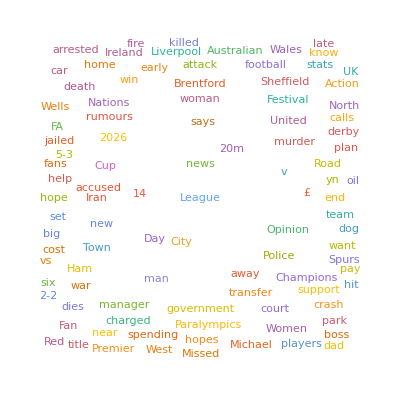

```mathematica
WordCloud[StringJoin[RandomSample[bbcArticlesHeadlines,500]]]
```

And use some of the integrated LLM functionality with the headlines:

```mathematica
emojify=LLMExampleFunction[{"Summarize the news article using emojis",{
"Rare red wind warning issued as Storm Darragh approaches"->"⛈️💨❗", 
"Nationwide fault causes delays across rail network"->"🇬🇧❌🚂",
"How citizen scientists are uncovering the secret lives of blue whales"->"🧑‍🔬🧐🐳"}}]
```

```mathematica
emojify[#]&/@RandomChoice[bbcArticlesHeadlines,5]
```

### Example: Scaling Up with Async Requests

Demonstrating our news example with another site, we can expand it by getting the body of the articles and not just the headlines. First, let’s get all the hyperlinks from the ESPN’s front page:

```mathematica
sportHyperlinks=Import["https://www.espn.co.uk/", "Hyperlinks"];
```

Then we can string match those that lead to articles, filtering out unrelated links:

```mathematica
sportArticleLinks=Flatten[StringCases[sportHyperlinks,RegularExpression["https://www.espn.co.uk/.*/story/.*"] (*StringExpression["https://www.espn.co.uk/", ___ ,"/story/", ___]*) ]];
```

```mathematica
Length[sportArticleLinks]
```

```mathematica
sportArticleLinks = RandomSample[sportArticleLinks,30];
```

Prepare an empty list that will hold all the variables:

```mathematica
sportArticleBodies={};
```

Now we have a few dozen articles. If we pass them to Import or URLRead, we will need to wait for them to be downloaded sequentially, which could take a long time. Wolfram Language is equipped with a lot of parallel computation functionality, which can greatly reduce the time needed for a list of independent computations. In the case of web fetching, parallel computation is often referred to as “asynchronous”, and the corresponding Wolfram Language function we can use for asynchronous web fetching is URLSubmit:

```mathematica
AbsoluteTiming[URLSubmit[#,HandlerFunctions-><|"TaskFinished"->(AppendTo[sportArticleBodies,Cases[ImportString[#Body,"XMLObject"],XMLElement["p",_,{content_String}]:>content,Infinity]]&)|>,HandlerFunctionsKeys->"Body"]&/@sportArticleLinks]
```

Check how many articles we have collected:

```mathematica
Length[sportArticleBodies]
```

Produce a word cloud again to see at a glance what’s been talked about today:

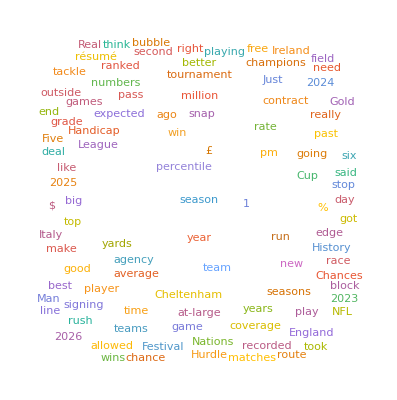

```mathematica
WordCloud[StringJoin[Flatten[sportArticleBodies]]]
```

Use TextCases with the "Country" argument to see which countries were mentioned today:

```mathematica
mentionedCountries=Flatten[TextCases[Flatten[sportArticleBodies], "Country"->"Interpretation"]]
```

Sort by the frequency of mentions:

```mathematica
countryFrequencies=ReverseSort[Counts[mentionedCountries]]
```

Word cloud of the countries:

```mathematica
WordCloud[#["Name"]&/@mentionedCountries/.{"United States"->"US","United Kingdom"->"UK"}]
```

A GeoBubbleChart from the frequencies:

```mathematica
GeoBubbleChart[Counts[mentionedCountries]]
```

Generate word cloud for top 3 countries:

```mathematica
GenClouds[articles_List]:=Module[{top3,unwantedwords,wordclouds},
top3=Keys[countryFrequencies[[;;3]]];
unwantedwords={"said"->"","says"->"","$"->"","£"->"","%"->"","’s"->"", RegularExpression["\\d{1,}"]->""};
wordclouds=Table[
WordCloud[DeleteStopwords[StringJoin[StringReplace[Map[
Function[If[ContainsAny[Interpreter["Country"][TextCases[#,"Country"]],{country}],#,Nothing]],StringRiffle[#]&/@articles],unwantedwords]]],ColorNegate[Binarize[country["Shape"],.95]],ImageSize->Large]
,{country,top3}];
Column[Transpose[{top3,wordclouds}]]
]
```

```mathematica
GenClouds[sportArticleBodies]
```

Use the article bodies to create a semantic search index:

```mathematica
ssind=CreateSemanticSearchIndex[Select[Flatten[sportArticleBodies],StringTrim[#]=!=""&]]
```

Use the created semantic search index as a dynamic prompt for your LLM interactions:

```mathematica
LLMSynthesize["why has England been in the news recently?",LLMEvaluator-><|"Prompts"->LLMPromptGenerator[ssind]|>]
```

## Automated Browsers, Parsing HTML

Importing the text from webpages with Import or URLRead is often enough for simple, static webpages. However, as you start visiting more complex, dynamic webpages, you will find that the information you are looking for might not be contained in the server response, even though you see it when you open the webpage in a web browser. There are multiple reasons why this might happen, but typically the server responds differently based on who or what is requesting the information. In many cases, websites load content dynamically with JavaScript scripts, which can only run on web browsers, so an HTML request for the content is unlikely to give you the full webpage.

If the website only serves the information you need when it is requested by a web browser, the solution is to use an automated web browser. Wolfram Language has built-in functionality to start and manage web browser sessions programmatically.

### Starting a Web Session

The first thing we need to do is start a web session. We will want to store that web session in a variable, since it is an object that we will be passing around every time we want to interact with it. We can start a web session in the following way:

```mathematica
session=StartWebSession["Chrome"]
```

Normally, these web browser sessions are run purely programmatically, without opening a graphical window for the browser (i.e. headlessly), but during development you might want to have a visual window so you can see what is happening. When you are satisfied that your web browser actions are being followed correctly, you can add the Visible->False option to StartWebSession, which will hide the browser window.

### WebExecute

With the session now open and its object stored in a variable, we can start interacting with it programmatically. The main function we are going to be using is WebExecute, which takes the web session as the first argument and an operation to be performed on that session as the second argument. For example, if we want to go to a specific webpage in our session, we can do it with:

```mathematica
WebExecute[session,"OpenPage"->"http://www.example.com"]
```

There is a wide range of actions that WebExecute can take. Here, we will focus on locating and extracting elements. On a basic level, all webpages are a combination of HTML, CSS and script files. We can use the structure of each of those to locate the elements that we are interested in. Let’s start by looking at how to grab HTML elements that we are interested in with WebExecute:

```mathematica
h1element=WebExecute[session,"LocateElements"->"Tag"->"h1"]
```

All elements located with "LocateElements" are WebElementObject instances. To extract the text contained in them, we can pass them to the "ElementText" option:

```mathematica
WebExecute[session,"ElementText"->h1element]
```

Let’s navigate to a website with a slightly more complicated structure:

```mathematica
WebExecute[session,"OpenPage"->"http://quotes.toscrape.com"]
```

The easiest way to get an idea of the structure of the website, and therefore of the location of the elements you are interested in, is to use the web inspector option in your browser, which allows you to point at different parts of the current webpage you are on and inspect their underlying HTML structure. The current page we are on contains quotes located in <span> elements.

-Graphics-

To get those, we can use the "LocateElements" option of WebExecute, specifying that we want elements that match a certain HTML tag, in this case, <span>:

```mathematica
allSpans=WebExecute[session,"LocateElements"->"Tag"->"span"];
```

And then get all <span> instances where the value for the "class" attribute is "text":

```mathematica
allQuotes=Map[
If[StringMatchQ[ WebExecute[session,"ElementAttribute"->{#,"class"}],"text"],(*If the element's class is "text"*)
WebExecute[session,"ElementText"->#],(*get its text*)
Nothing]& (*else: do nothing*)
, allSpans]
```

Now we have all the quotes in a list. Let’s get the author names, which are located in <small> HTML elements:

```mathematica
allAuthors=WebExecute[session,"LocateElements"->"Tag"->"small"];
```

Put everything together in an association:

```mathematica
quotesThread=AssociationThread[allQuotes,Map[WebExecute["ElementText"->#]&,allAuthors]]
```

And get a random quote from our list:

```mathematica
quoteOfTheDay=
With[
{n = Once[RandomInteger[{1,Length[quotesThread]}]]},Framed[StringJoin[Keys[quotesThread][[n]],"\n— ",quotesThread[[n]]]]]
```

When you are done with your session, remember to delete it with DeleteObject to avoid having unused processes running in the background (especially easy to forget if you’re running the browser headlessly):

```mathematica
DeleteObject[session]
```

### Example: Headless Browsers and String Cleaning

Sometimes, we want to transform the data we find online into a different format. In this example, we will take some tabular data from a Wikipedia page and present it as an interactive map. Specifically, we are interested in the blood type distribution in European countries.

#### Starting Up a Browser Session

Start up our headless browser with Visible->False, navigate to the relevant wiki page and extract the element with tag <table>:

```mathematica
ses=StartWebSession["Chrome",Visible->False];
```

```mathematica
WebExecute[ses,"OpenPage"->"https://en.wikipedia.org/wiki/Blood_type_distribution_by_country"];
```

```mathematica
table=WebExecute[ses,"LocateElements"->"Tag"->"table"];
```

#### Extracting the Relevant Elements (in This Case: The Second <table>)

Get the text of the second table (for this specific webpage, there is an empty element with the <table> tag that gets added to our list):

```mathematica
rawTable=WebExecute[ses,"ElementText"->table[[2]]];
```

#### String Cleaning

Now, we do some data cleaning that is specific to the webpage. We are mixing StringExpression and RegularExpression instances to extract the country names from the table:

```mathematica
countryList=StringTrim[#]&/@
(StringReplace[#,"["~~(DigitCharacter..)|(LetterCharacter..)|"citation needed"~~"]"->""]&/@StringCases[rawTable,RegularExpression["(.*)\\s(\\d{1,}.*,\\d{3})\\s(.*)"]->"$1"]);
```

Then we take out the information related to a specific blood type, in this case A+ and A-, and we store it in a list:

```mathematica
aPlus=StringDelete[StringSplit[StringCases[rawTable,RegularExpression["(.*)\\s(\\d{1,}.*,\\d{3})\\s(.*)"]->"$3"]," "][[All,2]],"%"];
```

```mathematica
aMinus=StringReplace[#,"n/a"->"NA"]&/@StringDelete[StringSplit[StringCases[rawTable,RegularExpression["(.*)\\s(\\d{1,}.*,\\d{3})\\s(.*)"]->"$3"]," "][[All,6]],"%"];
```

```mathematica
(* a = aPlus + aMinus *)
a=(ToExpression[#]&/@aPlus)+(ToExpression[#]&/@aMinus);
```

Then we create an association thread which associates the proportion of people with A blood type to the country name:

```mathematica
assoc=AssociationThread[countryList,a]
```

Finally, we take the names of the European countries and interpret them as entities:

```mathematica
europeCountriesNames=#["Name"]&/@=[europe countries];
```

```mathematica
europeCountriesEntities=Interpreter["Country"][#]&/@Intersection[Keys[assoc],europeCountriesNames];
```

```mathematica
aBloodType=assoc[#]&/@Intersection[Keys[assoc],europeCountriesNames];
```

This gives us the final association:

```mathematica
geoData=AssociationThread[europeCountriesEntities,aBloodType]
```

#### Final Plot

Then we can pass our final association to GeoHistogram to produce a map:

```mathematica
GeoHistogram[geoData,"Country",PlotLegends->{Placed[BarLegend[Automatic],Below],Placed["Proportion of people with A blood type",Top]},PlotTheme->"Scientific",GeoRange->=[europe],ImageSize->Full,Frame->True]
```

```mathematica
DeleteObject[ses]
```

### Example: Headless Browsers, Manipulating Webpages

In many cases, the data that we are interested in exists in different places, making unified analysis difficult. In this example, we will look at the Association of Tennis Professionals (ATP), which provides a lot of data about the tennis players on tour. This data, however, is split between different pages (at least four). If we want to do any meaningful analysis, we need to visit each webpage, collect the data and finally put it in a single dataset.

#### Serve Stats

We’ll start with the statistics related to serves. Open up a web browser and navigate to the serve stats webpage:

```mathematica
session=StartWebSession["Chrome"];
```

```mathematica
WebExecute[session,"OpenPage"->"https://www.atptour.com/en/stats/leaderboard?boardType=serve&timeFrame=52week&surface=all&versusRank=all&formerNo1=false"];
```

We see our first challenge: when we open the webpage, we see the cookies banner first, which is preventing us from further actions. Since we don’t want to do this manually, we can use the methods in WebExecute to achieve that, but first we need to locate the button. By inspecting the webpage, we see that the cookies button is located in a <button> tag, so get those first:

```mathematica
buttonTags = WebExecute[session,"LocateElements"->"Tag"->"button"];
```

There are a lot of <button> elements on a webpage, and we only need one of them. For each <button> element, we check if its text is equal to “Accept All Cookies”, and if it’s not, we discard it, which should leave us with only the <button> element that we care about:

```mathematica
cookiesButton=If[WebExecute[session,"ElementText"->#]=="Accept All Cookies",#,Nothing]&/@buttonTags;
```

Then we can use the "ClickElement" method of WebExecute to click the button:

```mathematica
WebExecute[session,"ClickElement"->First[cookiesButton]];
```

Our second challenge is: we see only the first 50 players. To see all, we need to click a button labeled “Load More” at the bottom of the page. This time, the “Load More” button is located in an <a> tag. We handle this in a similar way as the cookies button.

```mathematica
aTags=WebExecute[session,"LocateElements"->"Tag"->"a"];
loadMoreButton=If[WebExecute[session,"ElementText"->#]=="Load More",#,Nothing]&/@aTags;
WebExecute[session,"ClickElement"->First[loadMoreButton]];
```

Once all the players are loaded, we can extract the information that we care about. In this case, each row in the table is in a <tr> element, so we get that:

```mathematica
servetrTags=WebExecute[session,"LocateElements"->"Tag"->"tr"];
```

And we clean it up with a RegularExpression:

```mathematica
serveStats=StringCases[WebExecute["ElementText"->#],RegularExpression["(^\\d{1,})\\n(.*)\\n(\\d{3}.\\d)\\s(.*?%)\\s(.*?%)\\s(.*?%)\\s(.*?%)\\s(\\d{1,}.\\d{1})\\s(\\d{1,}.\\d{1})"]->{"$1","$2","$3","$4","$5","$6","$7","$8","$9"}]&/@servetrTags[[2;;]];
```

```mathematica
servesTab=ToTabular[Apply[<|
"Serve ranking"->Interpreter["Number"][#1],
"Name"->#2,
"Serve rating"->Interpreter["Number"][#3],
"% 1st serve"->Interpreter["Percent"][#4],
"% 1st serve points won" ->Interpreter["Percent"][#5],
 "% 2nd serve points won"->Interpreter["Percent"][#6],
"% Service games won"->Interpreter["Percent"][#7],
"Avg. aces/match"->Interpreter["Number"][#8],
"Avg. double faults/match"->Interpreter["Number"][#9]|>&,#]
&/@Flatten[serveStats,1]]
```

```mathematica
DeleteObject[session]
```

#### Return Stats

Since this page is almost identical to the previous one, we follow the same procedure. The only difference is that the table contains fewer elements, so our final function that extracts the information from the table is slightly modified:

```mathematica
(* start the session and open the page *)
session=StartWebSession["Chrome"];
WebExecute[session,"OpenPage"->"https://www.atptour.com/en/stats/leaderboard?boardType=return&timeFrame=52week&surface=all&versusRank=all&formerNo1=false"];

(* wait for page to load, and click "Cookies" button *)
Pause[3];
buttonTags = WebExecute[session,"LocateElements"->"Tag"->"button"];
cookiesButton=If[WebExecute[session,"ElementText"->#]=="Accept All Cookies",#,Nothing]&/@buttonTags;
WebExecute[session,"ClickElement"->First[cookiesButton]];

(* wait for page to load, and click "Load More" button *)
Pause[3];
aTags=WebExecute[session,"LocateElements"->"Tag"->"a"];
loadMoreButton=If[WebExecute[session,"ElementText"->#]=="Load More",#,Nothing]&/@aTags;
WebExecute[session,"ClickElement"->First[loadMoreButton]];
```

```mathematica
returntrTags=WebExecute[session,"LocateElements"->"Tag"->"tr"];
returnStats=StringCases[WebExecute["ElementText"->#],RegularExpression["(^\\d{1,})\\n(.*)\\n(\\d{3}.\\d)\\s(.*?%)\\s(.*?%)\\s(.*?%)\\s(.*?%)"]->{"$1","$2","$3","$4","$5","$6","$7"}]&/@returntrTags[[2;;]];
returnsTab=ToTabular[Apply[<|
"Return ranking"->Interpreter["Number"][#1],
"Name"->#2,
"Return rating"->Interpreter["Number"][#3],
"% 1st serve return points won"->Interpreter["Percent"][#4],
"% 2nd serve return points won" ->Interpreter["Percent"][#5],
 "% return games won"->Interpreter["Percent"][#6],
"% break points converted"->Interpreter["Percent"][#7]|>&,#]&/@Flatten[returnStats,1]]
```

```mathematica
DeleteObject[session]
```

#### Under Pressure Stats

This is the same type of webpage as before, so copy/paste the procedure:

```mathematica
(* start the session and open the page *)
session=StartWebSession["Chrome"];
WebExecute[session,"OpenPage"->"https://www.atptour.com/en/stats/leaderboard?boardType=pressure&timeFrame=52week&surface=all&versusRank=all&formerNo1=false"];

(* wait for page to load, and click "Cookies" button *)
Pause[3];
buttonTags = WebExecute[session,"LocateElements"->"Tag"->"button"];
cookiesButton=If[WebExecute[session,"ElementText"->#]=="Accept All Cookies",#,Nothing]&/@buttonTags;
WebExecute[session,"ClickElement"->First[cookiesButton]];

(* wait for page to load, and click "Load More" button *)
Pause[3]; 
aTags=WebExecute[session,"LocateElements"->"Tag"->"a"];
loadMoreButton=If[WebExecute[session,"ElementText"->#]=="Load More",#,Nothing]&/@aTags;
WebExecute[session,"ClickElement"->First[loadMoreButton]];
```

```mathematica
(* Get data and format data *)
pressuretrTags=WebExecute[session,"LocateElements"->"Tag"->"tr"];
pressureStats=StringCases[WebExecute["ElementText"->#],RegularExpression["(^\\d{1,})\\n(.*)\\n(\\d{3}.\\d)\\s(.*?%)\\s(.*?%)\\s(.*?%)\\s(.*?%)"]->{"$1","$2","$3","$4","$5","$6","$7"}]&/@pressuretrTags[[2;;]];pressureTab=ToTabular[Dataset[Apply[<|
"Under pressure ranking"->Interpreter["Number"][#1],
"Name"->#2,
"Under pressure rating"->Interpreter["Number"][#3],
"% break points converted"->Interpreter["Percent"][#4],
"% break points saved" ->Interpreter["Percent"][#5], 
"% tie breaks won"->Interpreter["Percent"][#6],
"% deciding sets won"->Interpreter["Percent"][#7]
|>&,#]&/@Flatten[pressureStats,1]]]
```

```mathematica
DeleteObject[session]
```

#### Rankings

The final page we care about is slightly different. First, all the players are listed automatically, so there is no need to look for a “Load More” button to click. We open up our browser and navigate to the webpage:

```mathematica
session=StartWebSession["Chrome"];
```

```mathematica
WebExecute[session,"OpenPage"->"https://www.atptour.com/en/rankings/singles"];
```

##### Getting the Countries

There are two things that we are interested in on this webpage: the players’ rankings and their countries. Since getting the countries is a bit more complicated, let’s start with that. All of the little flags beside the player’s image are located in <use> elements, which we can leverage:

```mathematica
flags=WebExecute[session,"LocateElements"->"Tag"->"use"];
```

Each use element has a “href” attribute leading to the flag itself, looking something like <use href="/assets/atptour/assets/flags.svg#flag-ita">. We can exploit the consistent structure with regular expressions to get everything after "flag-", which is essentially a three-letter code for the country (e.g. “ita”).

```mathematica
countryCodes=Flatten[StringCases[RegularExpression[".*#flag-(.*)"]:>"$1"][WebExecute[session,"ElementAttribute"->{#,"href"}]&/@flags]];
```

Now we have a list of three-letter country codes that we need to convert to actual country entities. The built-in Interpreter function can do a lot of the heavy lifting even with three-letter inputs. We can test:

```mathematica
Interpreter["Country"]["ita"]
```

However, in some cases, it might fail:

```mathematica
Interpreter["Country"]["cro"]
```

Let’s create a helper function that will take our countryCodes and return country entities. In it, we want to try interpreting the country code with Interpreter; if that fails, we want to use a more flexible tool like an LLM:

```mathematica
interpretCountry[code_String]:=Module[{wolframInterpretation,llmInterpretation,country},
wolframInterpretation=Interpreter["Country"][code];
llmInterpretation=LLMFunction["Which country is `1`. Respond only with the country name"];
country=If[FailureQ[wolframInterpretation],Interpreter["Country"][llmInterpretation[code]],wolframInterpretation];
If[FailureQ[country],Missing,country]
]
```

We can now map our new helper function to our country codes to get a list of countries:

```mathematica
countries=Map[interpretCountry,countryCodes]
```

##### Getting the Rankings

Get all <a> elements:

```mathematica
anchors=WebExecute[session,"LocateElements"->"Tag"->"a"];
```

Check if there is a player contained in each <a> element. <a> elements containing players have a “href” attribute, which we can represent as a string expression. We check if each element in “anchors” matches that expression, and we discard it if it does not:

```mathematica
(* this will take a bit *)
playerAnchors=If[
StringContainsQ[
WebExecute[
session,"ElementAttribute"->{#,"href"}],"https://www.atptour.com/en/players/"~~___~~"overview"],#,Nothing]&/@anchors//Quiet;
```

Now that we have the anchors that contain players, we can extract their text:

```mathematica
rankings=WebExecute[session,"ElementText"->#]&/@playerAnchors/.""->Nothing;
```

Since the player names are already ordered by the way they appear on the webpage, we don’t need to extract their rankings; we can simply append Range[100] to the first 100 names:

```mathematica
rankingsTab=ToTabular[Apply[<|
"World ranking"->Interpreter["Number"][#1],
"Name"->#2,
"Country"->#3
|>&,#]&/@Transpose[{Range[100],rankings[[;;100]],countries[[;;100]]}]]
```

```mathematica
DeleteObject[session]
```

#### Putting Everything Together

Once we have all the information we want from the different webpages, we can put it together in a single dataset:

```mathematica
JoinAcrossAll[list_,key_]:=Fold[JoinAcross[#1,#2,key]&,list];
JoinAcrossAll[list_,key_,joinspec_]:=Fold[JoinAcross[#1,#2,key,joinspec]&,list];
```

```mathematica
finalDataset=JoinAcrossAll[{rankingsTab,servesTab,returnsTab,pressureTab},"Name","Left"]
```

```mathematica
(*Export[FileNameJoin[NotebookDirectory[], "TennisDataset.mx"], finaldataset];*)
```

#### Exploration of the Data

Once we have the data in Wolfram Language, we can start using any of the thousands of built-in functions to get insights. For example, find out which country has the most representatives in the ATP Top 100:

```mathematica
ReverseSort[GroupBy[finalDataset,#Country &,Length]]
```

As well as world rankings, players are ranked across three other categories: serves, returns and performance under pressure. Find the player with the biggest discrepancy between world ranking and serve ranking:

```mathematica
TakeLargestBy[
    finalDataset,
    Abs[#["World ranking"]-#["Serve ranking"]]&,
    1
]
```

Find the players who can serve really well but can’t return:

```mathematica
TakeLargestBy[
    finalDataset,
    Abs[#["Serve ranking"]-#["Return ranking"]]&,
    3
]
```

Create a Manipulate object to explore scatter plots of different factors in the dataset:

```mathematica
With[{finaldataset=If[TabularQ[finalDataset],finalDataset,Import[FileNameJoin[NotebookDirectory[],"TennisDataset.mx"]]]},
Manipulate[
  Module[{factor1Values,factor2Values,playerNames,correlation},
    factor1Values=Normal[finaldataset[All,factor1]];
    factor2Values=Normal[finaldataset[All,factor2]];
    playerNames=Normal[finaldataset[All,"Name"]];
    correlation=Correlation[factor1Values,factor2Values];
    ListPlot[
      MapThread[
        Tooltip[{#1,#2},#3] &,
        {factor1Values,factor2Values,playerNames}
      ],
      AxesLabel->{factor1,factor2},
      PlotLabel->"Scatter Plot",
      ImageSize->Large,
      PlotMarkers->"🎾"
    ]
  ],
  {{factor1,"% 1st serve points won"},ColumnKeys[finaldataset],ControlType->PopupMenu},
  {{factor2,"Avg. aces/match"},ColumnKeys[finaldataset],ControlType->PopupMenu},
  TrackedSymbols:>{factor1,factor2},
SynchronousInitialization->False
]]
```

### Example: Headless Browsers, JavaScript Injections

As extensive as WebExecute is, there will eventually be some things that we would want to do that are not readily available. This is where the "JavascriptExecute" option comes in—it allows us to execute an arbitrary piece of JavaScript code in the browser that we are controlling. In practice, that opens up basically any web browser functionality.

In this example, we will see how we can load dynamic elements by scrolling to the bottom of the page to load more. Start our web session as usual:

```mathematica
session=StartWebSession["Chrome"];
```

Navigate to the resource repository. If you open this page separately, you will see that by default it loads only a few rows’ elements. When the user scrolls down to the bottom of the page, some more are loaded. If we are controlling the browser manually, we will keep scrolling to the bottom of the page until all elements are loaded. But how can we do that programmatically?

```mathematica
WebExecute[session,"OpenPage"->"https://resources.wolframcloud.com/ExampleRepository/"]
```

Since there is no “keep scrolling down” functionality baked into WebExecute, we can write a simple JavaScript loop to do what we need. Here, we are getting the height of the webpage before scrolling down to the bottom. If the new height of the page is larger than the one previously, this indicates that more things are loaded, so we repeat. We only stop when the height doesn’t change after the scroll:

```mathematica
WebExecute[session,"JavascriptExecute"->"let lastScrollHeight = 0;

// Create a hidden container to store links
let archiveDiv = document.createElement(\"div\");
archiveDiv.id = \"archived-links\";
archiveDiv.style.display = \"none\";
document.body.appendChild(archiveDiv);

const scrollAndCollect = () => {
    window.scrollTo(0, document.body.scrollHeight);

    setTimeout(() => {
        // Collect current visible links
        const links = document.querySelectorAll(\"a[href]\");
        links.forEach(link => {
            if (!archiveDiv.innerHTML.includes(link.href)) {
                const clonedLink = link.cloneNode(true);
                archiveDiv.appendChild(clonedLink);
                archiveDiv.appendChild(document.createElement(\"br\"));
            }
        });

        // Check if we need to scroll more
        if (document.body.scrollHeight > lastScrollHeight) {
            lastScrollHeight = document.body.scrollHeight;
            scrollAndCollect();
        }
        // else: done
    }, 1000); // wait 1 second after scroll
};

scrollAndCollect();"]
```

```mathematica
archivedLinks=WebExecute[session,"LocateElements"->"CSSSelector"->"#archived-links"];
```

```mathematica
allHyperlinks=WebExecute[session,"PageHyperlinks"];
Length[allHyperlinks]
```

And clean them up as usual:

```mathematica
allResourceLinks=Select[allHyperlinks,StringContainsQ["https://resources.wolframcloud.com/ExampleRepository/resources/"]];
Length[allResourceLinks]
```

Noticing this is significantly smaller than what we see.

```mathematica
DeleteObject[session]
```

#### Different approach

We can go to each category page to get the links without handling the webpage structure uncertainties.

```mathematica
(* this will take a while *)
categories={"astronomy","audio-processing","calculus","cellular-automata","chemistry","complex-systems","computer-science","computer-vision","control-systems","creative-arts","data-science","engineering","finance-economics","finite-element-method","food-nutrition","geography","geometry","graphs-networks","image-processing","life-sciences","machine-learning","mathematics","optimization","physics","probability-statistics","puzzles-and-recreation","quantum-computation","signal-processing","social-sciences","system-modeling","tabular-processing","text-language-processing","time-related-computation","video-processing","visualization-graphics"};

session2=StartWebSession["Chrome"];

allLinks=Flatten[Map[Function[cat,WebExecute[session2,"OpenPage"->"https://resources.wolframcloud.com/ExampleRepository/category/"<>cat];
Pause[3];
WebExecute[session2,"PageHyperlinks"]],categories]];

exampleLinks=Select[DeleteDuplicates[allLinks],StringContainsQ[#,"/resources/"]&];
```

```mathematica
RandomSample[exampleLinks,5]
```

Write a small function to extract the authors of all the contributed examples:

```mathematica
GetExampleContributors[allExamples_List,session_WebSessionObject]:=Module[{page,allContributors={}},
Do[
WebExecute[session,"OpenPage"->link];
page=WebExecute[session,"LocateElements"-> "CSSSelector"->"body > main > div.wrap > div > ul.source-metadata.publisher-info > li > span"];
AppendTo[allContributors, WebExecute[session, "ElementText"->page]];
,{link,allExamples}];
allContributors
]
```

Collect all the authors in a variable and clean up the web session:

```mathematica
(* this will take a while *)
allAuthors=Flatten[GetExampleContributors[exampleLinks,session2]];
```

Clean up the authors and tally them:

```mathematica
cleanedupAuthors=StringReplace[ToString[#]," Null"->""]&/@allAuthors;
Length[cleanedupAuthors]
```

378

```mathematica
ReverseSortBy[Tally[cleanedupAuthors],Last]
```

{{Wolfram Staff,235},{Wolfram Research, Quantum Computation Framework Team,33},{Stephen Wolfram,19},{Wolfram Controls Team,10},{Jeff Bryant,10},{Felipe Amorim,7},{Wolfram Research,6},{Phileas Dazeley-Gaist,6},{John McNally,6},{Robert Nachbar,4},{Jay Warendorff,4},{Gay Wilson,4},{Ali Hashmi,4},{Juan Ortiz,3},{Jason Biggs,3},{Jan Brugård,3},{Akram Masoud,3},{Soutick Saha,2},{Paco Jain (Wolfram Research),2},{Jessica Alfonsi,2},{Wolfram Research (Quantum Computation Framework Team),1},{Tommy Peters and Gay Wilson,1},{S. M. Blinder,1},{Sebastián Rodríguez, César Guerra,1},{Richard Hennigan (Wolfram Research),1},{Paco Jain,1},{Naman T.,1},{Isabel Skidmore, Tommy Peters and Gay Wilson,1},{Isabel Skidmore and Gay Wilson,1},{Daniel Sanchez,1},{Bruno Tenorio, Wolfram Research, Quantum Computation Framework Team,1},{Ali Hashmi, Wolfram Research,1}}

```mathematica
DeleteObject[session2]
```

## Conclusion

Between simple HTML requests with Import and URLRead, async requests with URLSubmit and automated web browsers with WebExecute, you have all the tools needed to build up web extraction workflows for virtually any website. The advantage of doing so in Wolfram Language, other than the accessibility and ease of use of these functions, is that once you get your data, you are able to immediately analyse, compute and visualise it with the thousands of built-in functions in Wolfram Language.

## Further Resources

#### Mathematica subscription

Check access
Free Trial & Subscription

#### Webinars and events

Wolfram U

#### Data science workflow

Workflow: Extract Textual Content from Webpages

Tech note: Strings and Characters

#### Public resources

Resources

## Thank you for listening!

Wednesday, March 18, 2026 · 15:00 GMT

Writing a Wolfram Language Function

Register: https://wolfr.am/1CHhsU415

## -Graphics-